```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/inhomo/MF_DR/Emin

```mathematica
λ300=75.8;
ν300=-482.^2;
c=1.7*10^-3*(10^3)^3;
```

```mathematica
sigma=ParallelTable[FindMinimum[{V[a1^2/2,6.5,N[i],320.,λ300,ν300,c]+Vvacuum[a1^2/2,6.5,300.],0<a1<30},{a1,20},WorkingPrecision->8][[2]][[1]][[2]]//Quiet,{i,0.1,40.,0.5}]
```

{18.482799,18.479546,18.479713,18.477154,18.47273,18.467122,18.460326,18.452345,18.443183,18.432844,18.421332,18.408658,18.394815,18.37982,18.363676,18.346392,18.327974,18.308431,18.287771,18.266003,18.243142,18.219185,18.194151,18.168051,18.140895,18.112694,18.08346,18.053205,18.021942,17.989684,17.956443,17.922232,17.887066,17.850959,17.813924,17.775976,17.737129,17.697398,17.656799,17.615345,17.573053,17.529938,17.486015,17.4413,17.395809,17.34956,17.302562,17.254836,17.206398,17.157263,17.107447,17.056967,17.005838,16.954077,16.9017,16.848723,16.795161,16.741031,16.686349,16.63113,16.575391,16.519147,16.462414,16.405207,16.347543,16.289435,16.2309,16.171953,16.112609,16.052883,15.992789,15.932343,15.871558,15.81045,15.749032,15.687318,15.625322,15.563059,15.50054,15.437781}

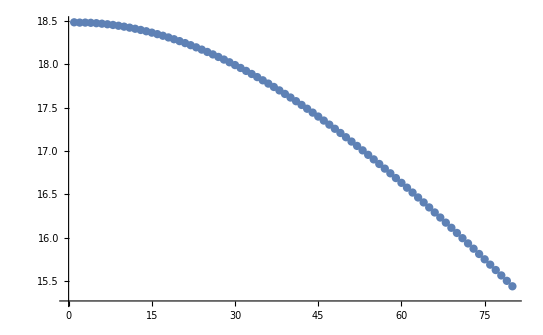

```mathematica
ListPlot[sigma]
```

```mathematica
Export["sigmamu320T.dat",sigma]
```

sigmamu320T.dat

```mathematica
T=Table[i,{i,0.1,40.,0.5}]
```

{0.1,0.6,1.1,1.6,2.1,2.6,3.1,3.6,4.1,4.6,5.1,5.6,6.1,6.6,7.1,7.6,8.1,8.6,9.1,9.6,10.1,10.6,11.1,11.6,12.1,12.6,13.1,13.6,14.1,14.6,15.1,15.6,16.1,16.6,17.1,17.6,18.1,18.6,19.1,19.6,20.1,20.6,21.1,21.6,22.1,22.6,23.1,23.6,24.1,24.6,25.1,25.6,26.1,26.6,27.1,27.6,28.1,28.6,29.1,29.6,30.1,30.6,31.1,31.6,32.1,32.6,33.1,33.6,34.1,34.6,35.1,35.6,36.1,36.6,37.1,37.6,38.1,38.6,39.1,39.6}

```mathematica
Export["T.dat",T]
```

T.dat

```mathematica
sigma={18.4827988213226213077`8.,18.4795456862686542365`8.,18.4797125009179019628`8.,18.4771541996729986579`8.,18.4727301117534175035`8.,18.4671217812202037578`8.,18.4603255853797207919`8.,18.4523446182347861111`8.,18.4431825307865935315`8.,18.4328435067337572661`8.,18.4213322193780122404`8.,18.4086577450428805491`8.,18.394815005170290334`8.,18.379819603024934338`8.,18.3636763180148179231`8.,18.3463919288952084229`8.,18.3279740706421527818`8.,18.3084308438958522913`8.,18.2877708389310953407`8.,18.2660031291224669303`8.,18.2431420765184491017`8.,18.2191847572963609991`8.,18.1941511913521907218`8.,18.1680509997572450231`8.,18.1408948382303805147`8.,18.1126939720225266228`8.,18.0834601343659677752`8.,18.0532054525597445149`8.,18.0219423836693124485`8.,17.9896837145853787376`8.,17.9564425153727036388`8.,17.9222321716983152839`8.,17.8870663037770292192`8.,17.8509587862402980818`8.,17.8139237670453702833`8.,17.7759755764520690491`8.,17.7371288012455394778`8.,17.6973981424989048605`8.,17.6567985676979084531`8.,17.6153451471579636234`8.,17.5730531495092172634`8.,17.5299379407456150659`8.,17.4860150448030964299`8.,17.4413000638729940306`8.,17.3958087196451707257`8.,17.3495602197679517076`8.,17.3025624158210398207`8.,17.2548362994588622144`8.,17.2063977469952220645`8.,17.1572626313494822625`8.,17.1074470143134931277`8.,17.0569668975980412995`8.,17.0058383371861054911`8.,16.9540774114162644537`8.,16.901700196091322681`8.,16.8487227149824754235`8.,16.7951610237969006789`8.,16.741031108817942652`8.,16.6863489072300197336`8.,16.6311302778425442739`8.,16.5753911081759746082`8.,16.5191471023180049826`8.,16.4624139521262762287`8.,16.4052072632667780283`8.,16.3475425264802609604`8.,16.2894351395233591973`8.,16.2309003947424272951`8.,16.171953441186946776`8.,16.1126093638200273972`8.,16.052883109386478111`8.,15.992789427249888945`8.,15.9323430125500493659`8.,15.8715583414577103838`8.,15.8104497994779826797`8.,15.749031576575045932`8.,15.6873177499499902865`8.,15.6253221793645931115`8.,15.5630585780704819854`8.,15.5005404870599381439`8.,15.43778128933541538`8.};
```

```mathematica
Export["./sigmamu320.dat",sigma]
```

./sigmamu320.dat